```mathematica
Nt = 455;(*151*)
ti = 0; tf =5; 
deltat = (tf - ti) /Nt ;
Nx = 455; (*151*)
(*xi = -2; xf = 8; *)
(*xi = 0; xf = 2*Pi;*)
xi = -40; xf = 40;
deltax = (xf - xi) / Nx;
c = 1;
r = c * (deltat / deltax^2)//N
k = .;
j  = .;
```

0.355469

```mathematica
deltax
```

16/91

```mathematica
(************************************************************************************************************************)
(*Set Up*)
(************************************************************************************************************************)
h = N[(2*Pi)/ (Nx),32];

Xp= N[Table[xm = xi + m *deltax, {m, 0, Nx}],32];

T = N[Table[tn = ti + n *deltat, {n, 0, Nt -1 }],32];
Xo = N[Table[xn = xi + n *deltax, {n, 0, Nx -1}],32];

X = N[(Xo-xi)*((2*Pi))/(xf-xi),32];

f[x_] = ⅇ^(- x^2+ⅈ x);
```

```mathematica
(************************************************************************************************************************)
(*Differentiation Matrix*)
(************************************************************************************************************************)
```

```mathematica
D1 = N[(2π)/(xf-xi)Table[If[ k≠ j, 1/2(-1)^(k - j)Csc[((k - j) * h)/2],0],{k,1,Nx},{j,1,Nx}],32];
D2 = deltat N[MatrixPower[D1,2],32];
```

```mathematica
L2 = N[Table[(NDSolve`FiniteDifferenceDerivative[Derivative[i],Xp, "DifferenceOrder"->2, PeriodicInterpolation -> True]@"DifferentiationMatrix"//Normal), {i,1,2}],32];
DL2 = N[Table[(-1)^i * L2[[i]] * (deltat)^i,{i,1,2}],32];
```

```mathematica
(*CN*)
UCN= N[Table[0, {n, 1, Nt}, {m, 1, Nx }],32];
UCN[[1,All]] = N[f[Xo],32];
UCN = N[UCN,32];
UCN = Chop[UCN, 10^(-307)];
UCN = Developer`ToPackedArray[UCN, Complex]; 
Developer`PackedArrayQ[UCN]


I1 = N[IdentityMatrix[Length[D1]],32];
A = N[I1 - ((ⅈ D2 / 4)),32];
B = N[I1 + ((ⅈ D2 / 4)),32];
MCN = N[Inverse[A].B,32];
EMCN = N[MCN - I1,32];
EMCN = Developer`ToPackedArray[EMCN, Complex]; 
Developer`PackedArrayQ[EMCN]

Do[UCN[[n+1,All]] = UCN[[n,All]] + (EMCN ).UCN[[n,All]], {n,1,Nt - 1 }];
```

True

True

```mathematica
(*RK2*)
(*URK2= N[Table[0, {n, 1, Nt}, {m, 1, Nx }],32];
URK2[[1,All]] = N[f[Xo],32];
URK2 = Chop[URK2, 10^(-307)];
URK2 = Developer`ToPackedArray[URK2, Complex]; 
Developer`PackedArrayQ[URK2]

IRK2 = N[IdentityMatrix[Length[D1]],32];

MRK2 = N[(IRK2 + (ⅈ D2 / 2) - ((1/2)*(D4/4))) -  ((1/6) * (ⅈ D6 / 8)),32];
EMRK2 = N[MRK2 - IRK2,32];

EMRK2= Developer`ToPackedArray[EMRK2, Complex]; 
Developer`PackedArrayQ[EMRK2]

Do[URK2[[n+1,All]] = URK2[[n,All]] + (EMRK2).URK2[[n,All]], {n,1,Nt - 1 }]*)
```

```mathematica
(*Partial Inversion*)
```

```mathematica
UP= N[Table[0, {n, 1, Nt}, {m, 1, Nx }],32];
UP[[1,All]] = N[f[Xo],32];
UP = Chop[UP, 10^(-307)];
UP = Developer`ToPackedArray[UP, Complex]; 
Developer`PackedArrayQ[UP]
```

True

```mathematica
Subscript[δ, i_,j_]:=KroneckerDelta[i,j];
```

```mathematica
selectwidth = 8;
diffOrder = 2;

deriv = 2;

(*The total number of points in the stencil*)
totalpoints = (2*selectwidth) + 1;

(*The middle point in the stencil*)
middlepoint = selectwidth + 1;

(*Set up the grid for the stencil*)
grid=x0+(Range[totalpoints]-middlepoint)Δx;

(LP=NDSolve`FiniteDifferenceDerivative[Derivative[deriv],grid,"DifferenceOrder"->diffOrder]@"DifferentiationMatrix"//Normal);

(*define r:=Δt/(Δx^deriv)*)
(*This is done so the M Matrix can be created symbollically and be created for any CFL Number by putting in a value for r*)
r=.;
LPX = LP*((-1)^deriv)*(r*(Δx)^deriv);

(*Manualy set up periodic boundary conditions because PeriodicInterpolation will remove removes a grid point on the end*)
(*Can use PeriodicInterpolation on the L Matrix if you add a +1 when defining the grid*)
gn = (LPX[[middlepoint,All]]//Normal)//Simplify//FullSimplify;
LPX = Table[RotateRight[gn,i],{i,-selectwidth,selectwidth}];
LPX = LPX//.{r -> (deltat / (deltax)^deriv)};

(*Set up Identity Matrix*)
IP=IdentityMatrix[Length[LPX]];

(*Generate a Crank–Nicolson M Matrix for the stencil*)
(Mn=Inverse[IP-(ⅈ * LPX)/4 ].(IP+(ⅈ * LPX)/4));

(*Take the middle row from this Crank-Nicolson M Matrix*)
fn=(Mn[[middlepoint,All]]//Normal)//Simplify//FullSimplify;


(*Generate a M Matrix from the L matrix for the stencil*)
MP = Table[0,{i,1,Nx},{j,1,Nx}];
  
(*WITH Periodic Boundary Conditions*)
MP = Table[Sum[(Subscript[δ, i,j+(middlepoint-k)])fn[[k]] + (Subscript[δ, i,(j-k)])fn[[middlepoint + k]],{k,selectwidth}] + Subscript[δ, i,j] fn[[middlepoint]] + Sum[(Subscript[δ, (i + Nx) - n,j])fn[[selectwidth - n]] + (Subscript[δ, (i + Nx) + n,(j + 2*Nx)])fn[[(middlepoint + 1) + n]]  ,{n,0,selectwidth - 1}],{i,0,Nx-1},{j,0,Nx-1}];

Ip = IdentityMatrix[Length[MP]];

EMP = MP - Ip;

EMP= Developer`ToPackedArray[EMP, Real]; 

Do[UP[[n+1,All]] = UP[[n,All]] + (EMP).UP[[n,All]], {n,1,Nt - 1 }];
```

```mathematica
fn[[1]]
```

1343652217162949377936315332568242863010/2148710550509701063108299736422494158060509919969-(13720741184870204566924033571447158267904 ⅈ)/2148710550509701063108299736422494158060509919969

```mathematica
(*Now we don't need D1 or DL to have 32 digit accuracy so can put it into a packed array*)
D1 = Developer`ToPackedArray[D1, Real];
D2=Developer`ToPackedArray[D2/deltat,Real];
```

```mathematica
(************************************************************************************************************************)
```

```mathematica
(*Energy*)
```

```mathematica
(************************************************************************************************************************)
```

```mathematica
(*CN*)
FCN = Table[0,{i,1,Nt},{j,1,Nx}];
FCN = Developer`ToPackedArray[FCN, Real];
intCN = Table[0,{i,1,Length[FCN[[All,1]]]}];
intCN = Developer`ToPackedArray[intCN, Real];
GCN = Table[0,{i,1,Nt},{j,1,Nx}];
GCN = Developer`ToPackedArray[GCN, Real];
GintCN = Table[0,{i,1,Length[FCN[[All,1]]]}];
GintCN = Developer`ToPackedArray[GintCN, Real];
Do[
FCN[[i]] = Conjugate[UCN[[i,All]]](UCN[[i,All]])//Re;

intCN[[i]] = (2π)/Nx Total[FCN[[i,All]]];
GCN[[i]] = -0.5Conjugate[UCN[[i,All]]](D2.UCN[[i,All]])//Re;

GintCN[[i]] = (2π)/Nx Total[GCN[[i,All]]]
,{i,1,Length[FCN[[All,1]]]}];
```

```mathematica
(*RK2*)
(*FRK2= Table[0,{i,1,Nt},{j,1,Nx}];
FRK2 = Developer`ToPackedArray[FRK2, Real];
intRK2 = Table[0,{i,1,Length[FRK2[[All,1]]]}];
intRK2 = Developer`ToPackedArray[intRK2, Real];
GRK2= Table[0,{i,1,Nt},{j,1,Nx}];
GRK2 = Developer`ToPackedArray[GRK2, Real];
GintRK2 = Table[0,{i,1,Length[FRK2[[All,1]]]}];
GintRK2 = Developer`ToPackedArray[GintRK2, Real];
Do[
FRK2[[i]] = Conjugate[URK2[[i,All]]](URK2[[i,All]])//Re;

intRK2[[i]] = (2π)/Nx Total[FRK2[[i,All]]];
GRK2[[i,All]] =-0.5 Conjugate[URK2[[i,All]]](D2.URK2[[i,All]])//Re;

GintRK2[[i]] = (2π)/Nx Total[GRK2[[i,All]]]
,{i,1,Length[FRK2[[All,1]]]}];
(*ListPlot[{Transpose[{T,intRK2}]},PlotRange->{All,{0,8}},Joined->True]*)*)
```

```mathematica
(*Partial Inversion*)
FP= Table[0,{i,1,Nt},{j,1,Nx}];
FP = Developer`ToPackedArray[FP, Real];
intP = Table[0,{i,1,Length[FP[[All,1]]]}];
intP = Developer`ToPackedArray[intP, Real];
GP= Table[0,{i,1,Nt},{j,1,Nx}];
GP = Developer`ToPackedArray[GP, Real];
GintP = Table[0,{i,1,Length[FP[[All,1]]]}];
GintP = Developer`ToPackedArray[GintP, Real];
Do[
FP[[i]] = Conjugate[UP[[i,All]]](UP[[i,All]])//Re;

intP[[i]] = (2π)/Nx Total[FP[[i,All]]];
GP[[i,All]] =-0.5 Conjugate[UP[[i,All]]](L2[[2]].UP[[i,All]])//Re;

GintP[[i]] = (2π)/Nx Total[GP[[i,All]]]
,{i,1,Length[FP[[All,1]]]}];
```

```mathematica
probErrorLD2=Abs[GintCN-GintCN[[1]]];
(*probErrorRK2=Abs[GintRK2-GintRK2[[1]]];*)
probErrorP = Abs[GintP - GintP[[1]]];
```

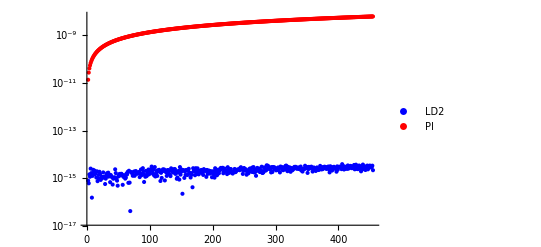

```mathematica
ListLogPlot[{probErrorLD2,probErrorP},PlotStyle->{Blue, Red},PlotLegends->{"LD2","PI"}]
```

```mathematica
energyErrorLD2 = Abs[intCN - intCN[[1]]];
(*energyErrorRK2 = Abs[intRK2 - intRK2[[1]]];*)
energyErrorP = Abs[intP - intP[[1]]];
```

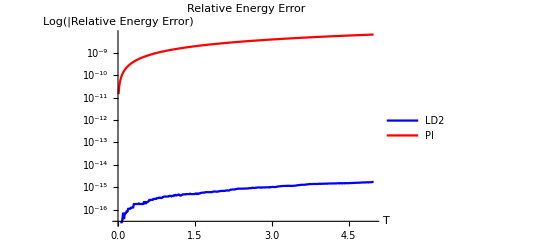

```mathematica
ListLogPlot[{Transpose[{T,energyErrorLD2}], Transpose[{T,energyErrorP}]},PlotStyle->{Blue, Red},PlotLegends->{"LD2","PI"},AxesLabel->{"T","Log(|Relative Energy Error)"},PlotLabel->"Relative Energy Error",PlotRange->{{ti,tf},{0,Max[energyErrorP]}},Joined->True]
```

```mathematica
(************************************************************************************************************************)
(*L1 Error*)
(************************************************************************************************************************)
```

```mathematica
fexact[t_,x_] = 1/(√(1+2 ⅈ t))Exp[(-(x-ⅈ/2)^2)/(1+2ⅈ t)-1/4];
Uexact = Table[fexact[T[[i]],Xo[[j]]],{i,1,Nt},{j,1,Nx}];
Uexact = Chop[N[Uexact], 10^(-307)];
Uexact = Developer`ToPackedArray[Uexact, Complex];
```

```mathematica
exacti={Re[fexact[0,Xo]],Im[fexact[0,Xo]]}//Transpose;
```

```mathematica
exactf={Re[fexact[T[[-1]],Xo]],Im[fexact[T[[-1]],Xo]]}//Transpose;
```

```mathematica
(*LD2*)
abserrLD2 = Abs[UCN-Uexact];
errorLD2 = Table[0,{i,1,Length[abserrLD2]}];
errorLD2 = Developer`ToPackedArray[errorLD2, Real];
Do[
errorLD2[[i]] = Norm[abserrLD2[[i,All]], 1] * deltax;
,{i,1,Length[errorLD2]}
];
(*ListLinePlot[Transpose[{T,errorLD2}],PlotRange->All]*)
```

```mathematica
(*RK2*)
(*abserrRK2 = Abs[URK2-Uexact];
errorRK2 = Table[0,{i,1,Length[abserrRK2]}];
errorRK2 = Developer`ToPackedArray[errorRK2, Real];
Do[
errorRK2[[i]] = Norm[abserrRK2[[i,All]], 1] * deltax;
,{i,1,Length[errorRK2]}
];*)
(*ListLinePlot[Transpose[{T,errorRK2}]]*)
```

```mathematica
(*Partial Inversion*)
abserrP = Abs[UP-Uexact];
errorP = Table[0,{i,1,Length[abserrP]}];
errorP = Developer`ToPackedArray[errorP, Real];
Do[
errorP[[i]] = Norm[abserrP[[i,All]], 1] * deltax;
,{i,1,Length[errorP]}
];
```

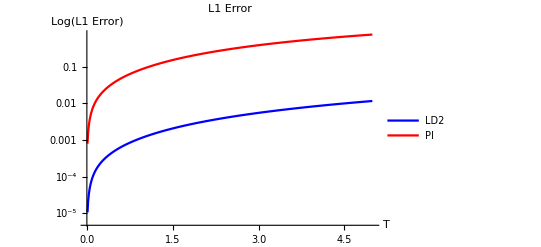

```mathematica
ListLogPlot[{Transpose[{T,errorLD2}],Transpose[{T,errorP}]},PlotRange->{{ti,tf},All}, PlotStyle->{Blue,Red},PlotLegends->{"LD2","PI"},AxesLabel->{"T","Log(L1 Error)" },PlotLabel->"L1 Error", Joined->True]
```

```mathematica
Animate[ListPlot[Table[UCN[[n+1, m+1]], {m,0,Nx  - 1}], PlotRange->All], {n,0,Nt - 1,1}, AnimationRunning->False]
```